## 7. teden

#### 1.naloga

```mathematica
Directory[]
```

\\Spin\PogacarT17$\_System\MyDocuments

```mathematica
SetDirectory[NotebookDirectory[]]
```

U:\ROM\ROM\7_teden

```mathematica
Directory[]
```

U:\ROM\ROM\7_teden

```mathematica
tabela = Import["rezultati.xlsx"]//First;
```

```mathematica
tabela//TableForm
```

Priimek | Ime | Skupina | Točke
Furlan | Luka | A | 93.
Karakaš | Alenka | A | 94.
Kočar | Petra | B | 44.
Kofol | Andraž | C | 34.
Kumar | Barbara | B | 67.
Logar | Mateja | A | 42.
Pance | Martin | B | 64.
Pleterski | Vesna | C | 30.
Trček | Valerija | B | 70.
Virant | Primož | C | 58.
Vesel | Polona | C | 66.
Žveglič | Katarina | A | 46.
Cvelbar | Janja | B | 39.
Furlan | Aleš | B | 36.
Iskra | Sabina | A | 77.
Jerman | Katja | B | 100.
Karničar | Jaka | C | 26.
Korošec | Kristina | B | 86.
Kržišnik | Grega | B | 90.
Obrenović | Tatjana | C | 44.
Puncer | Primož | A | 57.
Ribnikar | Matjaž | A | 43.
Štemberger | Igor | B | 85.
Šubašič | Matej | C | 76.
Tekavčič | Aleksander | A | 34.
Tratnik | Mojca | B | 79.
Smrekar | Andreja | A | 38.
Bezek | Tomaž | B | 38.

#### 2. naloga

```mathematica
Imena[podatki_]:= First[podatki]
```

```mathematica
Imena[tabela]
```

{Priimek,Ime,Skupina,Točke}

```mathematica
Podatki[podatki_]:=podatki//Rest
```

```mathematica
Podatki[tabela]//TableForm
```

Furlan | Luka | A | 93.
Karakaš | Alenka | A | 94.
Kočar | Petra | B | 44.
Kofol | Andraž | C | 34.
Kumar | Barbara | B | 67.
Logar | Mateja | A | 42.
Pance | Martin | B | 64.
Pleterski | Vesna | C | 30.
Trček | Valerija | B | 70.
Virant | Primož | C | 58.
Vesel | Polona | C | 66.
Žveglič | Katarina | A | 46.
Cvelbar | Janja | B | 39.
Furlan | Aleš | B | 36.
Iskra | Sabina | A | 77.
Jerman | Katja | B | 100.
Karničar | Jaka | C | 26.
Korošec | Kristina | B | 86.
Kržišnik | Grega | B | 90.
Obrenović | Tatjana | C | 44.
Puncer | Primož | A | 57.
Ribnikar | Matjaž | A | 43.
Štemberger | Igor | B | 85.
Šubašič | Matej | C | 76.
Tekavčič | Aleksander | A | 34.
Tratnik | Mojca | B | 79.
Smrekar | Andreja | A | 38.
Bezek | Tomaž | B | 38.

```mathematica
IndeksStolpca[podatki_,stolpec_]:= Position[podatki, stolpec] // Last//Last
```

```mathematica
IndeksStolpca[tabela, "Ime"]
```

2

```mathematica
Stolpec[podatki_,stolpec_]:= Transpose[podatki][[stolpec]]
```

```mathematica
Stolpec[tabela, 4]
```

{Točke,93.,94.,44.,34.,67.,42.,64.,30.,70.,58.,66.,46.,39.,36.,77.,100.,26.,86.,90.,44.,57.,43.,85.,76.,34.,79.,38.,38.}

```mathematica
PovprecjeTock[podatki_]:=Mean[Rest[Stolpec[podatki, 4]]]
```

```mathematica
PovprecjeTock[tabela]
```

59.1429

```mathematica
RazlicneVrednosti[podatki_,stolpec_]:= Union[Rest[Stolpec[podatki, stolpec]]]
```

```mathematica
RazlicneVrednosti[tabela, 3]
```

{A,B,C}

```mathematica
Vrstica[podatki_,i_]:=Podatki[podatki][[i ]]
```

```mathematica
Vrstica[tabela, 5]
```

{Kumar,Barbara,B,67.}

#### 3. naloga

```mathematica
OcenaZaMeje[{za6_,za7_,za8_,za9_,za10_},tocke_]:= If[tocke<za6, 0, If[tocke<za7, 6, If[tocke<za8, 7, If[tocke<za9, 8, If[tocke<za10, 9, 10]]]]]
```

```mathematica
OcenaZaMeje[{50,60,70,80,90}, 56]
```

6

```mathematica
Ocene[podatki_,meje_]:= Module[{ocene}, 
ocene = {};
For[i=1,i<=Length[Rest[Stolpec[podatki, 4]]], i++,ocene=Append[ocene,  OcenaZaMeje[meje,Rest[Stolpec[podatki, 4]][[i]]]]];
ocene
]
```

```mathematica
Ocene[tabela, {50,60,70,80,90}]
```

{10,10,0,0,7,0,7,0,8,6,7,0,0,0,8,10,0,9,10,0,6,0,9,8,0,8,0,0}

#### 4. naloga

```mathematica
DodajStolpec[podatki_,ime_,podStolpec_]:= Append[Transpose[podatki], Prepend[podStolpec, ime]] // Transpose
```

```mathematica
podatkiOcene = DodajStolpec[tabela, "Ocena", Ocene[tabela,{50,60,70,80,90}]] // TableForm
```

Priimek | Ime | Skupina | Točke | Ocena
Furlan | Luka | A | 93. | 10
Karakaš | Alenka | A | 94. | 10
Kočar | Petra | B | 44. | 0
Kofol | Andraž | C | 34. | 0
Kumar | Barbara | B | 67. | 7
Logar | Mateja | A | 42. | 0
Pance | Martin | B | 64. | 7
Pleterski | Vesna | C | 30. | 0
Trček | Valerija | B | 70. | 8
Virant | Primož | C | 58. | 6
Vesel | Polona | C | 66. | 7
Žveglič | Katarina | A | 46. | 0
Cvelbar | Janja | B | 39. | 0
Furlan | Aleš | B | 36. | 0
Iskra | Sabina | A | 77. | 8
Jerman | Katja | B | 100. | 10
Karničar | Jaka | C | 26. | 0
Korošec | Kristina | B | 86. | 9
Kržišnik | Grega | B | 90. | 10
Obrenović | Tatjana | C | 44. | 0
Puncer | Primož | A | 57. | 6
Ribnikar | Matjaž | A | 43. | 0
Štemberger | Igor | B | 85. | 9
Šubašič | Matej | C | 76. | 8
Tekavčič | Aleksander | A | 34. | 0
Tratnik | Mojca | B | 79. | 8
Smrekar | Andreja | A | 38. | 0
Bezek | Tomaž | B | 38. | 0

```mathematica
Export["ocene.xlsx", podatkiOcene]
```

ocene.xlsx

#### 5. naloga

```mathematica
BinCounts[Ocene[tabela, {50,60,70,80,90}]]
```

{0,13,0,0,0,0,0,2,3,4,2,4}

prva cifra je krneki, 2. je število 0, 8. število 7 ...

```mathematica
urejeneOcene = Sort[Ocene[tabela, {50,60,70,80,90}]];
porazdelitevOcen[ocene_] := Module[{negativna, šestice, sedmice, osmice, devetice, desetice},
negativna = Count[ocene, 0];
šestice = Count[ocene, 6];
sedmice = Count[ocene, 7];
osmice = Count[ocene, 8];
devetice = Count[ocene, 9];
desetice = Count[ocene, 10];
{negativna, šestice, sedmice, osmice, devetice, desetice}
]
```

```mathematica
porazdelitevOcen[Ocene[tabela, {50,60,70,80,90}]]
```

{13,2,3,4,2,4}

#### 6. naloga

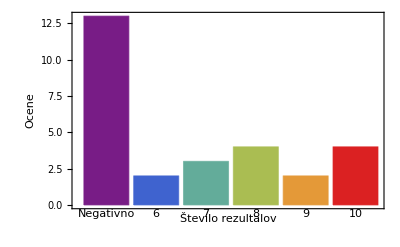

```mathematica
stolpicni = BarChart[porazdelitevOcen[Ocene[tabela, {50,60,70,80,90}]],  ChartStyle->"Rainbow", PlotLabel->None, ChartLabels->Placed[{"Negativno", 6, 7, 8, 9, 10}, Below], Frame->True, FrameLabel->{{ "Ocene", ""},{"Število rezultalov", "Ocene pri pisnem izpitu"}}]
```

```mathematica
Export["stolpicni.pdf", stolpicni]
```

stolpicni.pdf

#### 7. naloga

```mathematica
porazdelitev = porazdelitevOcen[Ocene[tabela, {50,60,70,80,90}]]
```

{13,2,3,4,2,4}

```mathematica
delezi = DecimalForm[N[Map[(100 * #)/Apply[Plus, porazdelitev]&, porazdelitev]], 3]
```

{46.4,7.14,10.7,14.3,7.14,14.3}

```mathematica
zdruzi[napis_,delez_]:= StringJoin[{napis, ToString[delez]}]
```

```mathematica
zdruzi[{"Negativno", "6", "7", "8", "9", "10"}, delezi]
```

Negativno678910{46.4, 7.14, 10.7, 14.3, 7.14, 14.3}